```mathematica
r1={0,0,0};
r2={7,4,3};
r3={8,-2,1};
C1=.3;
C2=.4;

dC=.05;

Show[

Graphics3D[{
RGBColor[0,1,1,1],
EdgeForm[],

Polygon[{
r1,r2,r3
}]
}],

Graphics3D[{
RGBColor[1,0,0,1],
EdgeForm[],

Polygon[{
(C1+0) r2+(C2+0) r3,
(C1+dC) r2+(C2+0) r3,
(C1+dC) r2+(C2+dC) r3,
(C1+0) r2+(C2+dC) r3
}+
Table[{0,0,.001},4]
]
}],

Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)
Background->Black,
ImageSize->.3{1920,1080}
]
```

-Graphics3D-

-Graphics3D-

```mathematica
{
(C1+0) r1+(C2+0) r2,
(C1+dC) r1+(C2+0) r2,
(C1+dC) r1+(C2+dC) r2,
(C1+0) r1+(C2+dC) r2,
}
```

{{5.6,3.2,2.4},{5.6,3.2,2.4},{6.3,3.6,2.7},{6.3,3.6,2.7},Null}

```mathematica
Graphics3D[{
RGBColor[0,1,1],
EdgeForm[],

Polygon[{
(C1+0) r1+(C2+0) r2,
(C1+dC) r1+(C2+0) r2,
(C1+dC) r1+(C2+dC) r2,
(C1+0) r1+(C2+dC) r2
}+
Table[{0,0,.01},4]
]
}]
```

-Graphics3D-

```mathematica
Polygon[{
(C1+0) r1+(C2+0) r2,
(C1+dC) r1+(C2+0) r2,
(C1+dC) r1+(C2+dC) r2,
(C1+0) r1+(C2+dC) r2
}+
Table[{0,0,.01},4]
]
```

Polygon[…]

```mathematica
Graphics3D[Polygon[{
(C1+0) r1+(C2+0) r2,
(C1+dC) r1+(C2+0) r2,
(C1+dC) r1+(C2+dC) r2,
(C1+0) r1+(C2+dC) r2
}+
Table[{0,0,.01},4]
]]
```

-Graphics3D-

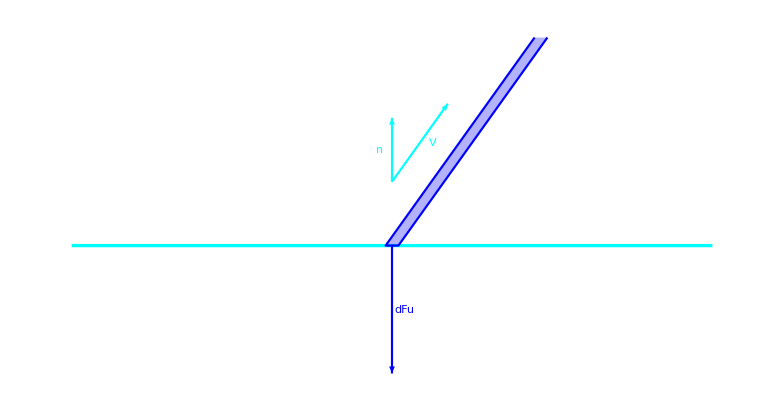

```mathematica
L=10;
l=.2;
d=.002;
V=Normalize[{5,7}];
faktorpušv=1.5;
faktpol=4;
n={0,1};
izh={0,1};
Fu={0,-2};
velikostčrk=5;


Show[

Graphics[{
RGBColor[0,1,1,1],
Thickness[1.5d],

Line[L/2{{-1,0},{1,0}}]
}],

Graphics[{
RGBColor[0,0,1,1],
Thickness[d],

Line[{
faktpol V+{l/2,0},
{l/2,0},
{-l/2,0},
faktpol V+{-l/2,0}
}]
}],



Graphics[{
RGBColor[0,0,1,.3],
EdgeForm[],

Polygon[{
{-l/2,0},
{l/2,0},
faktpol V+{l/2,0},
faktpol V-{l/2,0}
}]
}],

Graphics[{
RGBColor[0,1,1,1],
Arrowheads[.02],
Thickness[.002],
Style[Text[
"n",
izh+n/2+{-.2,0}
],
RGBColor[0,1,1],velikostčrk,Bold,FontFamily->"Comic Sans MS"],

Arrow[{izh,izh+n}]

}],

Graphics[{
RGBColor[0,1,1,1],
Arrowheads[.02],
Thickness[.002],
Style[Text[
"V",
izh+(faktorpušv V)/2+{.2,0}
],
RGBColor[0,1,1],velikostčrk,Bold,FontFamily->"Comic Sans MS"],

Arrow[{izh,izh+faktorpušv V}]

}],

Graphics[{
RGBColor[0,0,1,1],
Arrowheads[.02],
Thickness[.002],
Style[Text[
"dFu",
Fu/2+{.2,0}
],
RGBColor[0,0,1],velikostčrk,Bold,FontFamily->"Comic Sans MS"],

Arrow[{{0,0},Fu}]

}],

Boxed->False

]
```